```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)((17 + (Cos[theta])^2)/192/π)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-500, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
BOBmemScale2[scale1_, scale2_]:= Plot[MEMBOB[t, scale1, scale2]-MEMBOB[-500, scale1, scale2], {t, -100, 50}, PlotRange->{{-100, 50},{0.0, 0.1}}]
```

```mathematica
Manipulate[BOBmemScale2[a, b], {a, -0.9, 0.9}, {b, -0.9, 0.9}]
```

```mathematica
Eqn[α1_, α2_]:= NDSolve[{h'[t]==MEMBOB[t, α1, α2]-MEMBOB[-500, α1, α2], h[-60]==0},h, {t, -60,40}]
```

```mathematica
Inthmem[scale_] := Plot[{Evaluate[h[t]/.Eqn[scale,scale]]}, {t,-40,40}, PlotRange->{{-40, 40},{-1.0,2.0}}]
```

```mathematica
Manipulate[Inthmem[n] , {n, -0.9, 0.9}]
```

```mathematica
Res[t_, α1_, α2_] :=h[t] /. Eqn[α1, α2]
```

```mathematica
generateBOBmemdata[α1_, α2_, ti_, tf_, dt_]:=Res[#, α1, α2]& /@ Range[ti, tf, dt]
```

```mathematica
dataBoBmem[α1_, α2_, ti_, tf_, dt_] :=Transpose@{Range[ti, tf, dt], generateBOBmemdata[ α1, α2, ti, tf, dt][[All, 1]]}
```

```mathematica
parabolaBoBmem[ t_, α1_, α2_, ti_, tf_, dt_]:=Fit[dataBoBmem[α1, α2, ti, tf, dt],{1,x,x^2},x]/.x-> t;
```

```mathematica
ResMquad[t_, α1_, α2_, ti_, tf_, dt_] := Res[t, α1, α2] - parabolaBoBmem[t, α1, α2, ti, tf, dt]
```

```mathematica
ResFinal[ α1_, α2_, ti_, tf_, dt_] :=Part[ResMquad[#, α1, α2, ti, tf, dt]& /@ Range[ti, tf, dt],  All, 1]
```

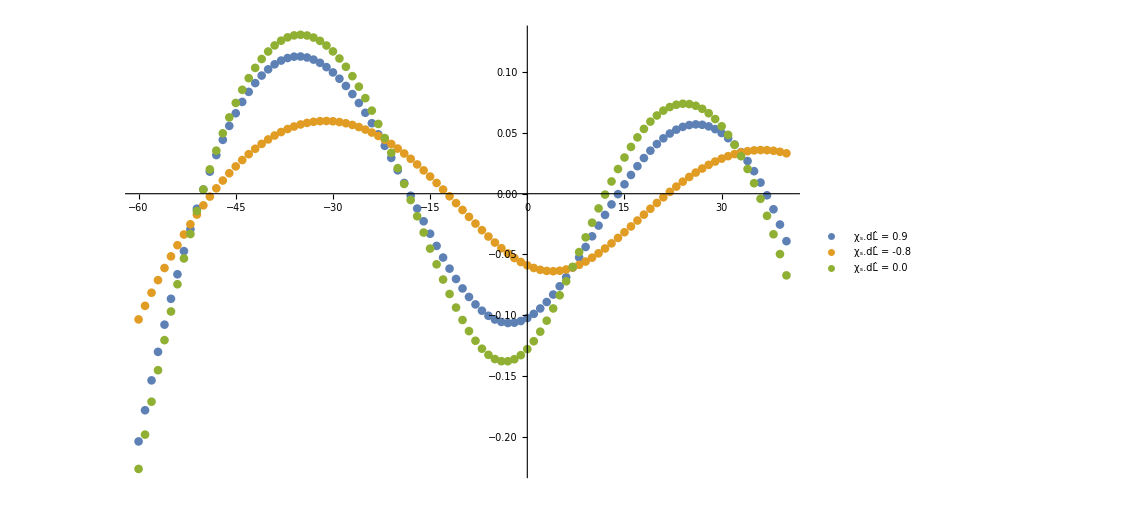

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60,40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,-0.8, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0,0, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = -0.8","χ_s.dL̂ = 0.0"},{0.120,0.87}]]
```

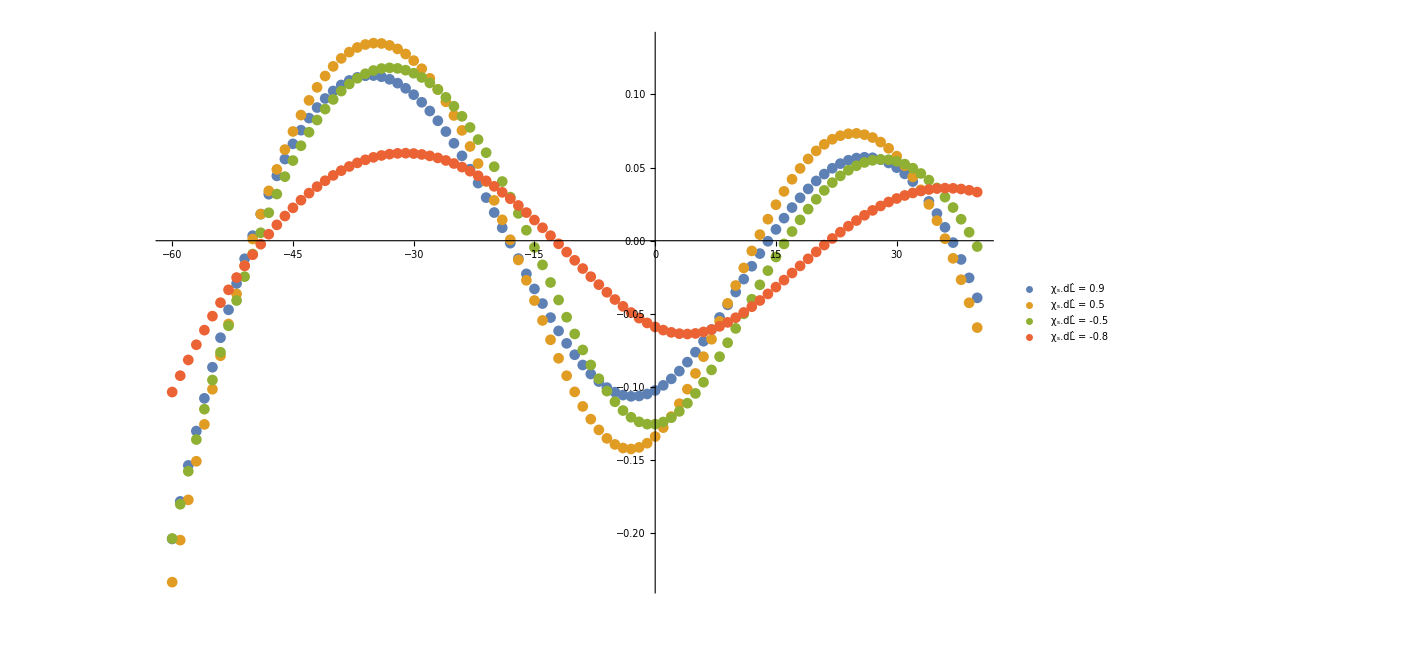

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60, 40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0.5,0.5, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.5,-0.5, -60, 40, 1 ]},Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,-0.8, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```

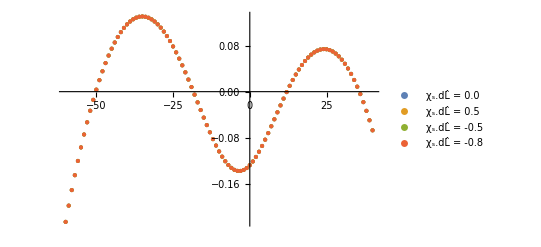

```mathematica
ListPlot[{Transpose@{Range[-60, 40, 1],ResFinal[ 0.0, 0.0, -60, 40,1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ 0.5,-0.5, -60, 40, 1 ]},  Transpose@{Range[-60, 40, 1],ResFinal[ -0.5,0.5, -60, 40, 1 ]},Transpose@{Range[-60, 40, 1],ResFinal[ -0.8,0.8, -60, 40, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.0", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```

```mathematica
DataResS0= Transpose@{Range[-60, 40, 1],ResFinal[ 0.0, 0.0, -60, 40,1 ]};
DataResS0p9= Transpose@{Range[-60, 40, 1],ResFinal[ 0.9, 0.9, -60, 40,1 ]};
DataResSm0p8= Transpose@{Range[-60, 40, 1],ResFinal[ -0.8, -0.8, -60, 40,1 ]};
```

```mathematica
PolyfitDataResS0 = Fit[DataResS0, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResS0p9 = Fit[DataResS0p9, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
PolyfitDataResSm0p8 = Fit[DataResSm0p8, {1, x, x^2, x^3, x^4, x^5, x^6, x^7},x];
```

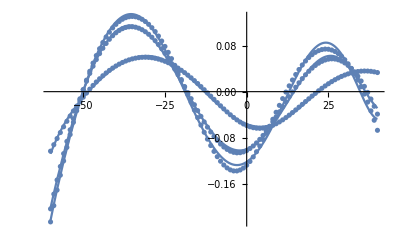

```mathematica
Show[ListPlot[DataResS0], Plot[PolyfitDataResS0, {x, -60 , 40}],ListPlot[DataResS0p9], Plot[PolyfitDataResS0p9, {x, -60 , 40}],ListPlot[DataResSm0p8], Plot[PolyfitDataResSm0p8, {x, -60 , 40}]]
```

```mathematica
(*Define Resedual function using polynomial fit*)
PolyResS0[t_]:= PolyfitDataResS0/.x-> t
PolyResS0p9[t_]:= PolyfitDataResS0p9/.x-> t
PolyResSm0p8[t_]:= PolyfitDataResSm0p8 /.x-> t
```

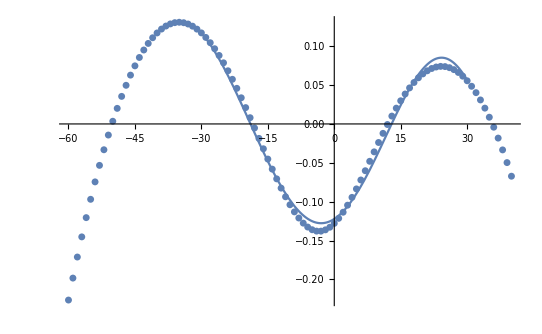

```mathematica
Show[ListPlot[DataResS0], Plot[PolyResS0[t], {t, -30 , 30}]]
```

```mathematica
(*Define function to take nonzero value only insude the observation time*)
ResS0[t_, ti_, tf_]:= Piecewise[{{PolyResS0[t], ti≤ t ≤tf}}, 0]
ResS0p9[t_, ti_, tf_]:= Piecewise[{{PolyResS0p9[t], ti≤ t ≤tf}}, 0]
ResSm0p8[t_, ti_, tf_]:= Piecewise[{{PolyResSm0p8[t], ti≤ t ≤tf}}, 0]
```

```mathematica
(*Taking analytical fourier transform *)
FTS0I1[ω]= Simplify[FourierTransform[ResS0[t, -55, 35], t, ω]Conjugate[FourierTransform[ResS0[t, -55, 35], t, ω]]//ComplexExpand];
FTS0p9I1[ω]= Simplify[FourierTransform[ResS0p9[t, -55, 35], t, ω]Conjugate[FourierTransform[ResS0p9[t, -55, 35], t, ω]]//ComplexExpand];
FTSm0p8I1[ω]= Simplify[FourierTransform[ResSm0p8[t, -55, 35], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -55, 35], t, ω]]//ComplexExpand];
FTS0I2[ω]= Simplify[FourierTransform[ResS0[t, -65, 45], t, ω]Conjugate[FourierTransform[ResS0[t, -65, 45], t, ω]]//ComplexExpand];
FTS0p9I2[ω]= Simplify[FourierTransform[ResS0p9[t, -65, 45], t, ω]Conjugate[FourierTransform[ResS0p9[t, -65, 45], t, ω]]//ComplexExpand];FTSm0p8I2[ω]= Simplify[FourierTransform[ResSm0p8[t, -65, 45], t, ω]Conjugate[FourierTransform[ResSm0p8[t, -65, 45], t, ω]]//ComplexExpand];
```

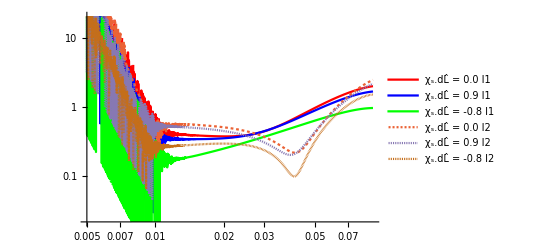

```mathematica
LogLogPlot[{Sqrt[Abs[FTS0I1[ω]]],Sqrt[Abs[FTS0p9I1[ω]]], Sqrt[Abs[FTSm0p8I1[ω]]] , Sqrt[Abs[FTS0I2[ω]]],Sqrt[Abs[FTS0p9I2[ω]]],Sqrt[ Abs[FTSm0p8I2[ω]]]}, {ω, 0.005, 0.09}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I1", "χ_s.dL̂ = 0.9 I1","χ_s.dL̂ = -0.8 I1", "χ_s.dL̂ = 0.0 I2", "χ_s.dL̂ = 0.9 I2","χ_s.dL̂ = -0.8 I2"},{0.850,0.7}],PlotStyle-> {Red, Blue,Green,Dashing[0.005],Dashing[0.002], Dashing[0.001]} , WorkingPrecision->MachinePrecision]
```

```mathematica
Sinf[t_]:= Piecewise[{{Sin[t]+ Sin[5t]+ Sin[40t], -8≤ t ≤8}}, 0]
Cosf[t_]:= Piecewise[{{Cos[3t], -8π≤ t ≤8π}}, 0]
SinCosf[t_]:= Piecewise[{{Cos[3t] + Sin[t], -π≤ t ≤π}}, 0]
```

```mathematica
FTSin[ω]= Simplify[FourierTransform[Sinf[t], t, ω]Conjugate[FourierTransform[Sinf[t], t, ω]]//ComplexExpand];
FTCos[ω]= Simplify[FourierTransform[Cosf[t], t, ω]Conjugate[FourierTransform[Cosf[t], t, ω]]//ComplexExpand];
FTSinCos[ω]= Simplify[FourierTransform[SinCosf[t], t, ω]Conjugate[FourierTransform[SinCosf[t], t, ω]]//ComplexExpand];
```

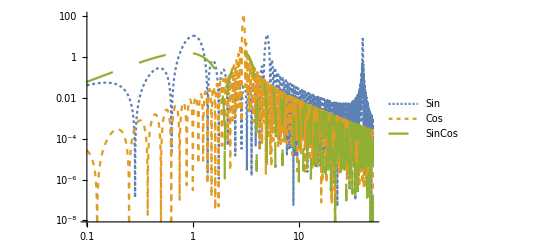

```mathematica
LogLogPlot[{Abs[FTSin[ω]], Abs[FTCos[ω]],Abs[FTSinCos[ω]]}, {ω, 0.1, 50}, PlotStyle-> {Dashing[0.005], Dashing[0.01], Dashing[0.05]}, PlotLegends->Placed[{"Sin", "Cos","SinCos"},{0.150,0.8}]]
```

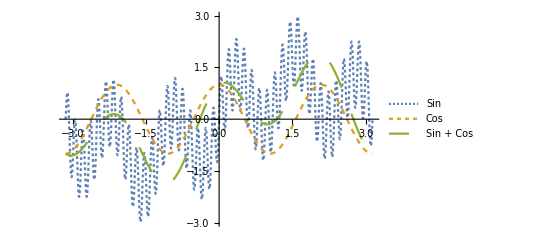

```mathematica
Plot[{Sinf[t], Cosf[t], SinCosf[t]}, {t, -π, π}, PlotStyle-> {Dashing[0.005], Dashing[0.01], Dashing[0.05]}, PlotLegends->Placed[{"Sin", "Cos","Sin + Cos"},{0.150,0.8}]]
```

```mathematica
ResS0period[t_, ti_, tf_]:=  Piecewise[{{PolyResS0[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
ResS0p9period[t_, ti_, tf_]:= Piecewise[{{PolyResS0p9[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
ResSm0p8period[t_, ti_, tf_]:=Piecewise[{{ PolyResSm0p8[t- tf - (tf-ti)Floor[(t)/(tf-ti)]], -200≤ t ≤200}}, 0]
```

```mathematica
Xt[t_]:=Piecewise[{{Sin[t], -π<t<π}}, 0]
Yt[t_]:=Piecewise[{{ Sin[t+1/4], -π<t< π}}, 0]
Rt[t_]:=Piecewise[{{ Sin[t+1/2], -π<t< π}}, 0]
St[t_]:=Piecewise[{{ Sin[t+3/4], -π<t< π}}, 0]
Tt[t_]:=Piecewise[{{ Sin[t+1], -π<t< π}}, 0]
```

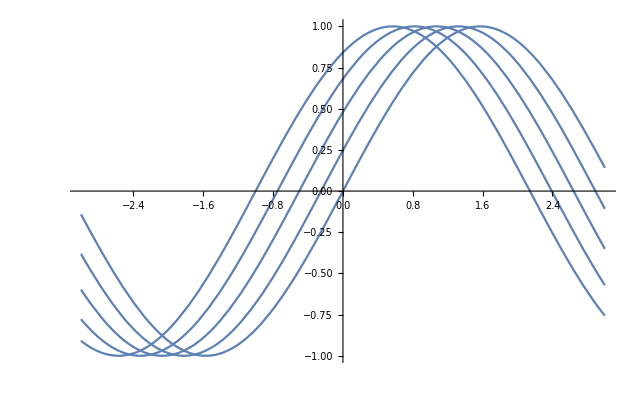

```mathematica
Show[Plot[Xt[t], {t, -3,3}], Plot[Yt[t], {t, -3,3}], Plot[Rt[t], {t, -3,3}], Plot[St[t], {t, -3,3}],  Plot[Tt[t], {t, -3,3}]]
```

```mathematica
FTXt[ω]= Sqrt[Simplify[FourierTransform[Xt[t], t, ω]Conjugate[FourierTransform[Xt[t], t, ω]]//ComplexExpand]]
FTYt[ω]= Sqrt[Simplify[FourierTransform[Yt[t], t, ω]Conjugate[FourierTransform[Yt[t], t, ω]]//ComplexExpand]]
FTRt[ω]= Sqrt[Simplify[FourierTransform[Rt[t], t, ω]Conjugate[FourierTransform[Rt[t], t, ω]]//ComplexExpand]]
FTSt[ω]= Sqrt[Simplify[FourierTransform[St[t], t, ω]Conjugate[FourierTransform[St[t], t, ω]]//ComplexExpand]]
FTTt[ω]= Sqrt[Simplify[FourierTransform[Tt[t], t, ω]Conjugate[FourierTransform[Tt[t], t, ω]]//ComplexExpand]]
```

√(2/π) √(Sin[π ω]^2/((-1+ω^2)^2))

√(2/π) √(((Cos[1/4]^2+ω^2 Sin[1/4]^2) Sin[π ω]^2)/((-1+ω^2)^2))

(√(-((-1+ω^2 (-1+Cos[1])-Cos[1]) Sin[π ω]^2)/((-1+ω^2)^2)))/(√π)

√(2/π) √(((Cos[3/4]^2+ω^2 Sin[3/4]^2) Sin[π ω]^2)/((-1+ω^2)^2))

√(2/π) √(((Cos[1]^2+ω^2 Sin[1]^2) Sin[π ω]^2)/((-1+ω^2)^2))

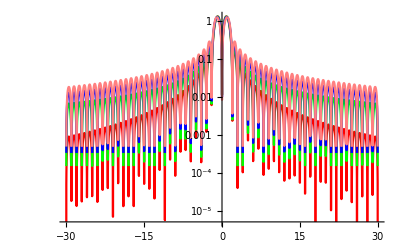

```mathematica
Show[LogPlot[FTXt[ω], {ω, -30, 30}, PlotStyle->{Red}], LogPlot[FTYt[ω], {ω, -30, 30}, PlotStyle->{Green}],  LogPlot[FTRt[ω], {ω,-30, 30}, PlotStyle->{Blue}],  LogPlot[FTSt[ω], {ω, -30, 30}, PlotStyle->{Pink}]]
```

```mathematica
Pt[t_]:=Piecewise[{{1, -3<t<3}}, 0]
Qt[t_]:=Piecewise[{{ Sin[1.5t], -3<t< 3}}, 0]
```

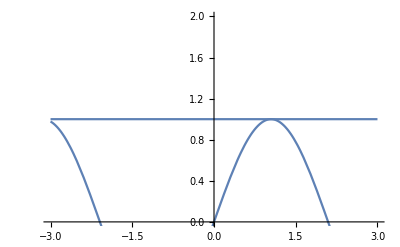

```mathematica
Show[Plot[Pt[t], {t, -3,3}], Plot[Qt[t], {t, -3,3}]]
```

```mathematica
FTPt[ω]= Sqrt[Simplify[FourierTransform[Pt[t], t, ω]Conjugate[FourierTransform[Pt[t], t, ω]]//ComplexExpand]]
FTQt[ω]= Sqrt[Simplify[FourierTransform[Qt[t], t, ω]Conjugate[FourierTransform[Qt[t], t, ω]]//ComplexExpand]]
```

√(2/π) √(Sin[3 ω]^2/ω^2)

√(((-1.36875 ω^2+0.608332 ω^4) Cos[3. ω]^2+(-0.143209+0.0636483 ω^2) Sin[3. ω]^2+ω (0.442737-0.196772 ω^2) Sin[6. ω])/((-2.25+1. ω^2)^3))

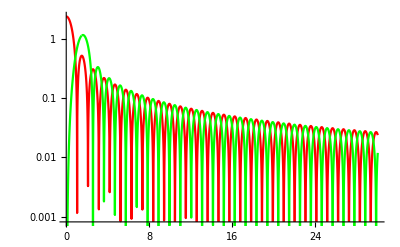

```mathematica
Show[LogPlot[FTPt[ω], {ω, 0, 30}, PlotStyle->{Red}], LogPlot[FTQt[ω], {ω, 0, 30}, PlotStyle->{Green}]]
```

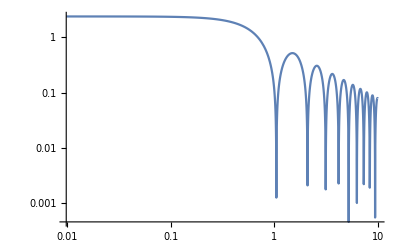

```mathematica
LogLogPlot[FTPt[ω], {ω, 0, 10}]
```

```mathematica
FourierTransform[Sin[f t], t, ω]
```

ⅈ √(π/2) DiracDelta[-f+ω]-ⅈ √(π/2) DiracDelta[f+ω]

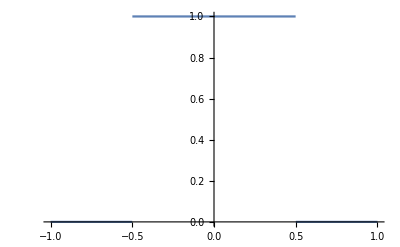

```mathematica
Plot[UnitBox[x], {x, -1,1}]
```

```mathematica
SinC[f_, ω_] :=FourierTransform[UnitBox[t]t, t, ω]
```

```mathematica
SinC[f, ω]
```

-(ⅈ (ω Cos[ω/2]-2 Sin[ω/2]))/(√(2 π) ω^2)

```mathematica
D[SinC[f, ω], ω]
```

(ⅈ √(2/π) (ω Cos[ω/2]-2 Sin[ω/2]))/ω^3+(ⅈ Sin[ω/2])/(2 √(2 π) ω)

```mathematica
SinC[f, ω]Conjugate[SinC[f, ω]]//ComplexExpand
```

Cos[ω/2]^2/(2 π ω^2)-(2 Cos[ω/2] Sin[ω/2])/(π ω^3)+(2 Sin[ω/2]^2)/(π ω^4)

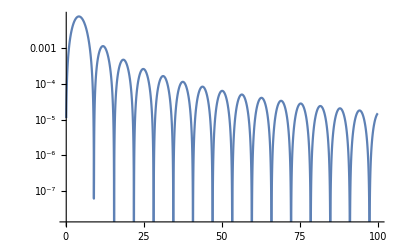

```mathematica
LogPlot[Cos[ω/2]^2/(2 π ω^2)-(2 Cos[ω/2] Sin[ω/2])/(π ω^3)+(2 Sin[ω/2]^2)/(π ω^4), {ω,0.1, 100}]
```

```mathematica
SinCPlot[f_] := LogPlot[SinC[f, ω]Conjugate[SinC[f, ω]]//ComplexExpand, {ω,-100, 100}]
```

```mathematica
Gt[t_, n_]:=Piecewise[{{t^n, -1<t<1}}, 0]
```

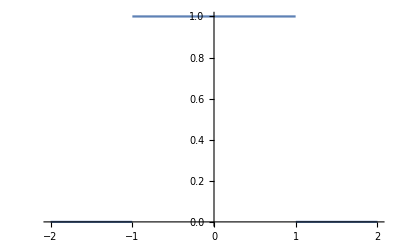

```mathematica
Plot[Gt[t, 0], {t, -2, 2}]
```

```mathematica
FTGt1[ω]= Simplify[FourierTransform[Gt[t, 1], t, ω]Conjugate[FourierTransform[Gt[t, 1], t, ω]]//ComplexExpand]
FTGt2[ω]= Simplify[FourierTransform[Gt[t, 2], t, ω]Conjugate[FourierTransform[Gt[t, 2], t, ω]]//ComplexExpand]
FTGt3[ω]= Simplify[FourierTransform[Gt[t, 3], t, ω]Conjugate[FourierTransform[Gt[t, 3], t, ω]]//ComplexExpand]
FTGt4[ω]= Simplify[FourierTransform[Gt[t, 4], t, ω]Conjugate[FourierTransform[Gt[t, 4], t, ω]]//ComplexExpand]
```

(2 (-ω Cos[ω]+Sin[ω])^2)/(π ω^4)

(2 (2 ω Cos[ω]+(-2+ω^2) Sin[ω])^2)/(π ω^6)

(2 (ω (-6+ω^2) Cos[ω]-3 (-2+ω^2) Sin[ω])^2)/(π ω^8)

(2 (4 ω (-6+ω^2) Cos[ω]+(24-12 ω^2+ω^4) Sin[ω])^2)/(π ω^10)

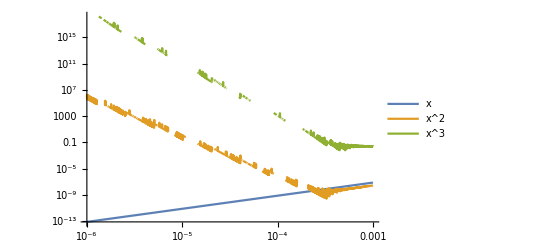

```mathematica
LogLogPlot[{FTGt1[ω], FTGt3[ω], FTGt4[ω]}, {ω, 0.000001, 0.001}, PlotLegends->Placed[{"x", "x^2","x^3"},{0.150,0.2}] ]
```

```mathematica
Limit[FTGt4[ω], ω-> 0]
Limit[FTGt3[ω], ω-> 0]
Limit[FTGt2[ω], ω-> 0]
```

2/(25 π)

0

2/(9 π)

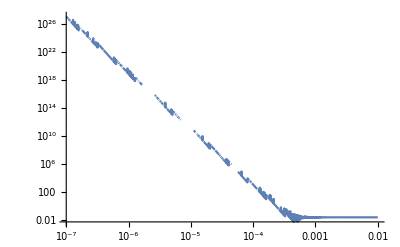

```mathematica
LogLogPlot[FTGt4[ω], {ω, 0.0000001, 0.01}]
```

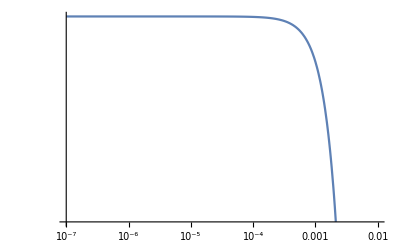

```mathematica
LogLogPlot[FTGt4[ω], {ω, 0.0000001, 0.01}, WorkingPrecision->40]
```

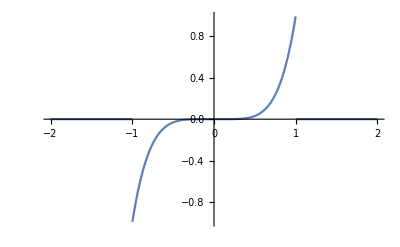

```mathematica
Plot[Gt[x,5], {x, -2,2}, PlotRange->Full]
```

```mathematica
ⅈ √(2/π) Simplify[D[Sin[ω-t]/(ω-t), {t,9}]]/.t-> 0
```

(ⅈ √(2/π) (-362880 ω Cos[ω]+60480 ω^3 Cos[ω]-3024 ω^5 Cos[ω]+72 ω^7 Cos[ω]-ω^9 Cos[ω]+362880 Sin[ω]-181440 ω^2 Sin[ω]+15120 ω^4 Sin[ω]-504 ω^6 Sin[ω]+9 ω^8 Sin[ω]))/ω^10

```mathematica
FullSimplify[(ⅈ √(2/π) (-362880 ω Cos[ω]+60480 ω^3 Cos[ω]-3024 ω^5 Cos[ω]+72 ω^7 Cos[ω]-ω^9 Cos[ω]+362880 Sin[ω]-181440 ω^2 Sin[ω]+15120 ω^4 Sin[ω]-504 ω^6 Sin[ω]+9 ω^8 Sin[ω]))/ω^10-(-(ⅈ √(2/π) (ω (362880-60480 ω^2+3024 ω^4-72 ω^6+ω^8) Cos[ω]-9 (40320-20160 ω^2+1680 ω^4-56 ω^6+ω^8) Sin[ω]))/ω^10)]
```

0

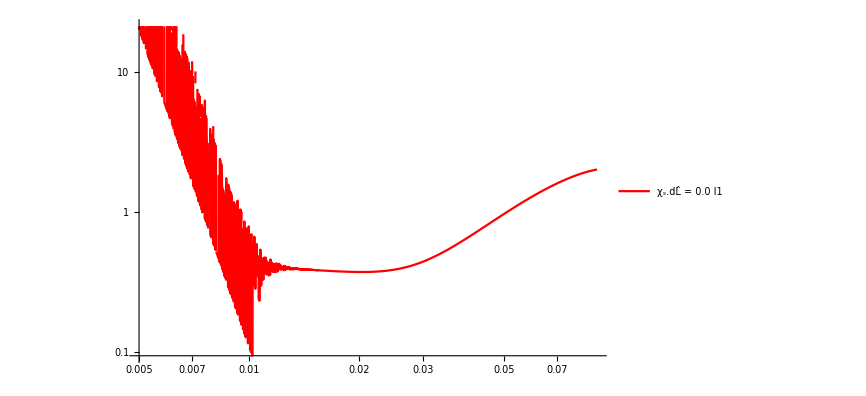

```mathematica
LogLogPlot[{Sqrt[Abs[FTS0I1[ω]]]}, {ω, 0.005, 0.09}, PlotLegends->Placed[{"χ_s.dL̂ = 0.0 I1"},{0.850,0.7}],PlotStyle-> {Red} ]
```

```mathematica
Gf[f_, n_]:= (-1)^n √(2/π)(I)^n D[Sin[f]/f, {f,n}]
```

```mathematica
Gf[f, 3]
```

ⅈ √(2/π) ((6 Cos[f])/f^3-Cos[f]/f-(6 Sin[f])/f^4+(3 Sin[f])/f^2)

```mathematica
Simplify[FourierTransform[Gt[t, 3], t, f]]
```

-(ⅈ √(2/π) (f (-6+f^2) Cos[f]-3 (-2+f^2) Sin[f]))/f^4

```mathematica
DiffGF[n_]:= Simplify[Gf[f, n]-Simplify[FourierTransform[Gt[t, n], t, f]]]
```

```mathematica
DiffGF[22]
```

0